# Mathematica 2 - Advanced Functions, Slash-dot, Prefix & Postfix Notation, Plotting Derivatives, Simplifying Expressions

Remember these three helpful tips:  

(1)  If things are NOT working as you would expect and you can’t spot why, it’s time to restart.  Go to Evaluation→Quit Kernel→Local. That shuts down the “kernel” (jprocessing engine) andclears everything; and Mathematica will automacally restart as soon as you execute a command.  Or, if you just want to end the current calculation (that is progressing v e r y  s l o w l y...) use Evaluation→Abort.

(2)  Make use of Mathematica’s online help. Click anywhere in a function name and press F1 to get information about the function.  Search for help topics by going to Help→Documentation Center. Remember the help documents are themselves active Mathematica documents, so you can execute code directly in the help pages.

(3) Mathematica cares a LOT about what types of brackets you use, and will not understand what you want if  you use the wrong ones.  Use parentheses ( ) for arethmatic grouping just as you would in your calculator; use [ ] square brackets for function calls and function definitions, and { } curly brackets to enclose lists of items.

A helpful way to start your worksheet is with a command that clears the memory but stops short of a full kernel reboot.  This way if you want to go back and re-do the commands in your worksheet, or if you happen to have several worksheets open at once, all you need to do is click on this line and begin again.

```mathematica
ClearAll["Global`*"]
```

This command erases all symbol definitions and clears assumptions so that they don’t interfere with what comes next.  Here the ‘ refers to the “current session” and * means “everything”

Delayed function assignments with :=

In Intro to Mathematica you learned the basics of how to define and refer to functions, such as this to define f(x)=5 x^2+2x:

```mathematica
f[x_] = 5 x^2 + 2x
```

2 x+5 x^2

```mathematica
f[3]
```

51

Sometimes functions are defined with  :=  instead of with  =.  This causes a subtle difference in the way Mathematica handles the function. With equals, the function is immediately defined as was specified by the right hand side of the equation. With a colon-equals, the function definition is postponed until it is actually called later. And it’s reevaluated each time it’s called. 

Here’s an example which illustrates this difference:

```mathematica
m=2;
fn[x_] = m x^2  (* immediate assignment -- evaluated right now, so fn(x) = 2 x^2 *)
fndelay[x_]:= m x^2   (* delayed assignment -- not evaluated until used later *)
fna[4]
fndelay[4]
```

2 x^2

fna[4]

32

Now change the value of m:

```mathematica
m=3;
fn[4]  (* uses the original value m=2 that was in force when the assignment was first made *)
fndelay[4]   (* reevaluated now using the current value of m *)
```

32

48

Things to notice: 

1. The semicolons at the ends of the m= statements suppress output from these statements.  Similarly, the function definition fndelay[x_] := m x^2  generates no output (because it’s not evaluated yet). In that respect it’s like there is a semicolon at the end of the line.

2. The function fn(x) was defined to be 2 x^2 for all time (or at least, until it gets redefined).

3. The function fndelay(x) was defined to be mx^2, NOT 2 x^2.  Each time the function fndelay(x) is used, Mathematica has to detect what the value of m is in order to evaluate the function. And so the value of fndelay(4) in the second call is different than the value of fndelay(4) in the first call.

4. However: If you had defined fn[x_] = m x^2 before assigning a set value to m, then fn(x) would be defined as mx^2, and would behave just like fndelay(x), even if you later fix m to have a particular value.  Take a look:

```mathematica
Clear[fn,fndelay,m]
fn[x_] = m x^2 
m=2;
fn[4]
m=3;
fn[4]
```

m x^2

32

48

Most of the time you won’t need to stress over the dfference in these ways of defining f(x).  For now, if a function isn’t behaving as you expect, remember this distinction and check to see if you should have used := instead of =. 

ALSO: The  :=  notation works for any type of assignment that you’d otherwise do with a regular equals sign, not just functions.

Slash-dot notation /.

As you learned in the Intro to Mathematica assignment, the arrow symbol → ( which you get by typing "-" followed by ">" ) can be used inside functions to specify parameters.  More generally, → defines a “rule” by which one quantity is replaced with another, and has very general usage when paired with a “slash-dot” to apply that rule to an expression:

```mathematica
5 x^2 + 2x  /. x->3
```

51

```mathematica
expr = 5 x^2 + 2x
```

2 x+5 x^2

```mathematica
expr /. x->3
```

51

```mathematica
expr/. x-> y^2
```

2 y^2+5 y^4

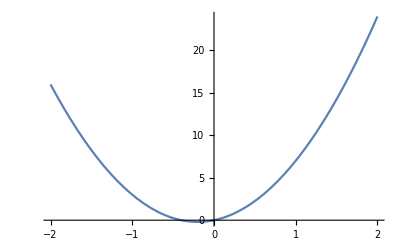

```mathematica
Plot[expr,{x,-2,2}]
```

Things to notice: 

1. Read the arrow symbol → as “replaced by.” Read “slash-dot” as the word “with”
So the command 5 x^2+2x  /. x→3”  translates as  “5 x^2+2x, with x replaced by 3”. So it gives you “5·3^2+2·3, or 51.  

2. Slash-dot commands have the general format: expression /. rule

3. Slash-dot can be used to make expressions behave a bit like functions.  The expression expr isn’t a function (it’s just the name of the expression), but using slash-dot we can evaluate it by replacing the variables it contains with numbers.

4. As shown in the   /. x→ y^2   example, you can use slash-dot to replace a variable with pretty much anything, including a function of another variable.

5. Slash-dot doesn’t change values permanently.  In the examples above, expr doesn’t change to 51 or become a function of y^2.  So the Plot function behaves as you might expect - you get the same thing as if you had typed in “Plot[5 x^2 + 2 x,{x,-2,2}].

Slash-dot usage with FindRoot and Solve. Slash-dot can be used to make the solutions to FindRoot and Solve look a bit more “normal”. Look at the difference between the outputs of these commands:

```mathematica
FindRoot[Cos[x]^2==x, {x,.5}]
```

{x→0.641714}

```mathematica
x /. FindRoot[Cos[x]^2==x, {x,.5}]
```

0.641714

```mathematica
Solve[3 x^2 == 4 (3 x - x^2) +5, x]  (* from Intro worksheet *)
```

{{x→1/7 (6-√71)},{x→1/7 (6+√71)}}

```mathematica
x /. %
```

{1/7 (6-√71),1/7 (6+√71)}

```mathematica
N[%]
```

{-0.346593,2.06088}

Things to notice: 

1. FindRoot and Solve return lists of rules as their output.  The fact that an output expression is a rule rather than a number is indicated by the arrow →. The output of the first FindRoot command is the rule “x replaced by 0.641714”.

2. The rules returned by those commands can be used as the “rules” part of a slash-dot command. So the second input can be read like this: “x, with x replaced by 0.641714”. This of course gives you just 0.641714.

#### Assignment 1. Three slash-dot tasks

(a) Use slash-dot notation to figure out what this complicated expression is equal to when x is 4:  1/(3 (1+x))-(-1 + 2x)/(6 (1-x +x^2))+2/(3(1 + (1/3) (-1 +2 x)^2)).  
(b) Figure out the expression in terms of y, given x = 2y (and simplify your result)
(c) Define the following two expressions: y_1=x sin(x) and y_2=e^x. When plotted, the two curves intersect in an infinite number of places. Use FindRoot to find the intersection that occurs closest to x=0, and use slash-dot to determine what the y-value of the intersection is without doing any copying & pasting of your own.

```mathematica
(* (a) *)
g[x]=1/(3 (1+x))-(-1 + 2x)/(6 (1-x +x^2))+2/(3(1 + (1/3) (-1 +2 x)^2))

g[x] /. x-> 4
```

1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2))

1/65

```mathematica
(* (b) *)
g[x] /. x -> 2y
Simplify[%]
```

1/(3 (1+2 y))-(-1+4 y)/(6 (1-2 y+4 y^2))+2/(3 (1+1/3 (-1+4 y)^2))

```mathematica
(* (c) *)
y1[x] = x*Sin[x];
y2 [x] = E^x;
x /. FindRoot[y1[x] == y2[x], {x,0}]
```

-0.727101

Postfix and Prefix notation

### Postfix notation //

In addition to the standard g[x] form for calling a function, Mathematica provides several different alternate forms for calling functions. One of these is the “postfix” form, indicated by two slashes: //.  The following two function calls are equivalent:

```mathematica
g[x]     (* function call in standard notation *)
x//g  (* equivalent shorthand call in "postfix" notation *)
```

The postfix notation is a bit like “Reverse Polish Notation” (RPN) if you have ever used an older HP calculator or are familiar with the concept of a “stack”.

```mathematica
Log[2.4]
```

0.875469

```mathematica
2.4 //Log  (* the same thing! *)
```

0.875469

```mathematica
N[Sin[1]]
```

0.841471

```mathematica
Sin[1] //N
```

0.841471

```mathematica
ArcSin[.7]  /Degree
```

44.427

Things to notice: 

1. The second log command can be read: “Consider the number 2.4.  Now take the log of it.”

2. The postfix method of forcing a numerical answer ( //N ) is extremely helpful.  Just tack it on to your command line after you realize you want a numerical value.

3. There’s not an easy way of specifying a second argument via postfix form. So if you want sin(1) to 50 decimal places it’s usually best to use something like N[Sin[1],50].

4. The constant “Degree” is equal to pi/180, the conversion factor for going from degrees to radians. To go from radians to degrees, you can divide by it. Its slash has nothing to do with postfix form; it’s simple division. But it’s included here because it sort of works to think of it as a “convert to degrees” postfix function.

### Prefix notation @

Another alternate way of calling a function is the “prefix” form, indicated by an at sign: @.  The following two function calls are equivalent:

```mathematica
g[x]     (* function call in standard notation *)
g@x      (* equivalent shorthand call in "prefix" notation *)
```

g[x]

g[x]

The expression "g@x" can be read as "g evaluated at x"

```mathematica
g[x_]=Sqrt[x/3];
g[13]
g@13
```

√(13/3)

√(13/3)

#### Assignment 2. Postfix and prefix calculations

(a) Calculate the numerical value of log(sin(sqrt(exp(7.3)))) using standard commands.
(b) Repeat, using only postfix commands.
(c) Repeat, using prefix form

```mathematica
(* (a) *)
Log[Sin[Sqrt[Exp[7.3]]]]
```

-0.356515

```mathematica
(* (b) *)
7.3 // Exp // Sqrt // Sin // Log
```

-0.356515

```mathematica
(* (c) *)
Log@Sin@Sqrt@Exp@7.3
```

-0.356515

#### Assignment 3. Using FindRoot to solve a transcendental equation... and using the result

Let x0 represent the value of x for which x = e^-x. This is a transcendental equation, an equation that has no closed-form solution (i.e. you can’t write an equation for x).  Determine x0 with FindRoot, and then calculate sin(x0) using slash-dot (and no copy-and-paste). Hint: when solving transcendental equations it's always good to start with a graph of the functions that represent the left and right hand sides of the equation, to give you a rough idea of the answer. The solution x0 is where the functions intersect, because that’s the place where the left and right hand sides of the equation equal each other.

Plotting Derivatives

To take a derivative, use the D command:

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Sin[x],x,x]
```

-Sin[x]

Take a moment to look over the Help file on this command (cursor on the D, click F1)

Something to be aware of:  Plot can handle so many different things that you may be tempted to plot a derivative like this:

```mathematica
f[x_]=1/Sin[x]^2;
diff=D[f[x],x];
Plot[D[f[x],x],{x,-2,2}]
```

The problem is that the Plot command works by calculating (x,y) points, then drawing lines between them.  And here it first calculates a numerical value for f[x], THEN tries to take the derivative - which makes no sense.

 To plot a derivative, calculate the derivative first, outside the Plot command.

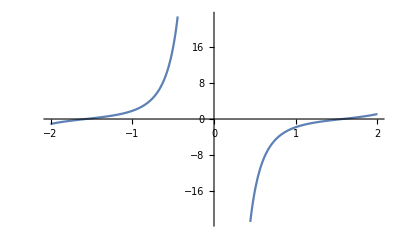

```mathematica
f[x_]=1/Sin[x]^2;
diff=D[f[x],x];
Plot[diff,{x,-2,2}]
```

Assignment 4: Derivatives

For each of the following, use a single D command:
(a) Find the decimal value of the second derivative of f(x) = 1/√(x^2+2), evaluated at x = 2.

(b) Plot P_3(x) along with its first derivative, from 0 to 20. Plot the P_3 function in blue and the derivative in red. P_n(x) is the “nth Legendre polynomial,” where Legendre polynomials are special functions which crop up in the solutions to the Schrodinger equation in 3 dimensions.  These are built-in functions within Mathematica (see LegendreP in help files). 

(c) Plot √(1+x^2) along with d^3/dx^3 √(1+x^2) , from -4 to 4. Plot the function in blue and the derivative in orange. Use either the option PlotLegends → “Expressions” or PlotLabels → “Expressions” to identify each plot.

(d) Plot3D (sin^2(x+y))/(x+y) along with ∂/(∂y)(∂/(∂x)(sin^2(x+y))/(x+y)) (or equivalently  ∂^2/(∂x∂y)(sin^2(x+y))/(x+y), from -π to π on both the x- and the y-axes. Plot the function in blue and the derivative in orange.

```mathematica
(* (a) *)
a4[x] = 1/(Sqrt[x^2 +2]);
D[a4[x],x,x] /. x->4;
Simplify[%]
```

5/(162 √2)

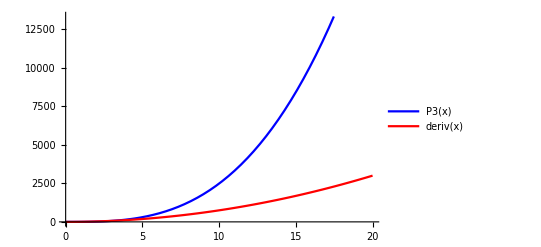

```mathematica
(* (b) *)
P3[x]=LegendreP[3,x];
deriv[x] = D[P3[x],x];
Plot[{P3[x],deriv[x]},{x,0,20},PlotStyle->{Blue,Red}, PlotLegends->"Expressions"]
```

```mathematica
(* (c) *)
c1[x] = Sqrt[1+x^2];
cD3[x] = D[c1[x],x,x,x];
Simplify[%];
Plot[{c1[x],cD3[x]},{x,-4,4}, PlotStyle->{Blue,Orange}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
(* (d) *)
d1[x,y]=((Sin[x+y])^2)/(x+y);
d2[x,y] = D[d1[x,y],x,y];
Simplify[%];
Plot3D[{d1[x,y],d2[x,y]},{x,Pi,-Pi},{y,Pi,-Pi},PlotStyle->{Blue,Orange}]
```

-Graphics3D-

Simplifying expressions / writing them in different forms.

```mathematica
Clear["'*"]
```

Simplify is a powerful command you will use a lot.  In the Wavefunctions worksheet you'll get some practice using it with assumptions

```mathematica
Cos[x]^2+Sin[x]^2
Simplify[%]
```

Cos[x]^2+Sin[x]^2

1

Use Expand to expand an expression.  If Simplify doesn’t get you what you want, try Expanding first, then Simplify

```mathematica
Expand[(x-2 y)^4]
```

x^4-8 x^3 y+24 x^2 y^2-32 x y^3+16 y^4

```mathematica
Expand[Cos[A+B]]
Expand[Cos[A+B],Trig->True]
```

Cos[A+B]

Cos[A] Cos[B]-Sin[A] Sin[B]

Expand just expands, it doesn’t simplify:

```mathematica
expr=(9 x^2-y^2)/(3x + y)
Expand[expr]
Simplify[expr]
```

(9 x^2-y^2)/(3 x+y)

(9 x^2)/(3 x+y)-y^2/(3 x+y)

3 x-y

Expand works only at the “top level” of expressions, and doesn’t expand sub-expressions.  Use ExpandAll for that

```mathematica
expr2=Sqrt[(1-x)^2]
Expand[expr2]
ExpandAll[expr2]
```

√((1-x)^2)

√((1-x)^2)

√(1-2 x+x^2)

Use Together to group terms over one common denominator.  Apart separates an expression into terms with simple denominators.  Factor factors the terms

```mathematica
expr=1/(x-a)^2+1/(x+a)^2
Together[expr]
Apart[%]
```

1/(-a+x)^2+1/(a+x)^2

(2 (a^2+x^2))/((a-x)^2 (a+x)^2)

1/(-a+x)^2+1/(a+x)^2

```mathematica
expr=-1+x-x^2+x^3
Factor[%]
```

-1+x-x^2+x^3

(-1+x) (1+x^2)

There is a deep connection between trigonometric functions of real variables and complex exponential functions and between hyperbolic trigonometric functions and exponential functions of a real variable.  In this course you will find yourself switching back and forth between these representations.  TrigToExp converts a trig expression into an exponential expression

```mathematica
TrigToExp[Tan[x]]
```

(ⅈ (ⅇ^(-ⅈ x)-ⅇ^(ⅈ x)))/(ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))

ExpToTrig converts an exponential into a trig or hyperbolic trig expression, and evaluates the trig terms if possible

```mathematica
ExpToTrig[Exp[I Pi/3]]
ExpToTrig[Exp[Pi/3]]
```

1/2+(ⅈ √3)/2

Cosh[π/3]+Sinh[π/3]

ComplexExpand: At times you may have a complicated algebraic expression that you need to separate into real and imaginary parts. If you had numbers, it would be no problem--you could just use the Re and Im commands.

```mathematica
complicatedz = ((3 + 4 I)/(2 - 5 I) + (1 + 3 I))/(2 + 2 I)
Re[%] //N
Im[%%] //N
```

125/116+(95 ⅈ)/116

1.07759

0.818966

But look what happens when you try to use Re and Im with an algebraic expression containing unknowns:

```mathematica
complicatedz= (a + b I)/(c - d I)
Re[%]
Im[%%]
```

(a+ⅈ b)/(c-ⅈ d)

Re[(a+ⅈ b)/(c-ⅈ d)]

Im[(a+ⅈ b)/(c-ⅈ d)]

Mathematica doesn’t know what to do, because it doesn’t know whether the numbers a ... d themselves are real or complex.  The ComplexExpand function comes to our rescue. It will algebraically separate z into real and imaginary parts, assuming that all of the unknown parameters are purely real numbers.

```mathematica
ComplexExpand[complicatedz] (* Notice how in the complicated expression, the real stuff comes first and everything that's multiplied by i comes second. *)
```

(a c)/(c^2+d^2)-(b d)/(c^2+d^2)+ⅈ ((b c)/(c^2+d^2)+(a d)/(c^2+d^2))

#### Assignment 5. Converting between exponential and sin/cos forms

(a) Use ExpToTrig to convert e^ix into trigonometric form, to verify that Mathematica “knows” Euler’s formula.
(b) Use ExpToTrig to convert e^x into trigonometric form. This is the analog of Euler’s formula for hyperbolic functions sinh(x) and cosh(x).
(c) Use TrigToExp to convert cos(x) and sin(x) into exponential form.
(d) Use TrigToExp to convert cosh(x) and sinh(x) into exponential form. Notice the similarity to the exponential forms of cosine and sine.
(e) Use Mathematica to take the complex conjugate of e^ix and then show that it is equal to cos(x)-isin(x) (rather than the awkward “cos[Conjugate[x]]- i sin[Conjugate[x]]”).  Don’t make explicit use of Assumptions to define x as real.

```mathematica
(* (a) *)
ExpToTrig[Exp[x]]
```

Cosh[x]+Sinh[x]

```mathematica
(* (b) *)
ExpToTrig[Exp[x]]
```

Cosh[x]+Sinh[x]

```mathematica
(* (c) *)
TrigToExp[Cos[x]]
TrigToExp[Sin[x]]
```

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
(* (d) *)
TrigToExp[Cosh[x]]
TrigToExp[Sinh[x]]
```

ⅇ^-x/2+ⅇ^x/2

-ⅇ^-x/2+ⅇ^x/2

```mathematica
(* (e) *)
Conjugate[Exp[I*x]]
Simplify[%]
TrigToExp[Cos[x]-I*Sin[x]]
```

ⅇ^(-ⅈ Conjugate[x])

ⅇ^(-ⅈ Conjugate[x])

ⅇ^(-ⅈ x)

Summary

The following functions were discussed in this worksheet, or are very closely related:
Working with functions: -> or → (Rule), /. (ReplaceAll), := (SetDelayed), //  (Postfix), @ (Prefix) 
Manipulating Algebraic functions: Simplify, Expand, Together, Apart, Factor, Collect, TrigToExp, ExpToTrig, ComplexExpand

Potentially useful summary/tutorial pages
Guide: Special Characters
Tutorial: Strings and Characters Overview
Guide: Constructing Lists
Guide: Elements of Lists
Guide: List Manipulation
Tutorial: Testing and Searching List Elements
Tutorial: Expressions

What to turn in
When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#4a-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 5).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.